```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/14/2010     

Assignment #2
Problem 2_a                                                    *)
```

```mathematica
Clear[a,b,fbas,f,fs,L,coeffs,fourier];
(*using a generic L until I can figure out how to introduce it as a variable*)
(*trying to figure out how to define functions as peicewise in mathematica*)
(*f[x_]:=x*(1+Abs[x])/;-1≤x<1;
f[x_]:=f[x+2]/;x≥1OR x<-1; 
f[1],f[3]  *)
```

```mathematica
L=1;
fbas[x_]:=(1+x)/;-L≤x<L
f[x_]:=fbas[Mod[x,2×L,-L]]
```

```mathematica
N[f[3]]
```

0.

```mathematica
(*Defining the function as peicewise*)
```

```mathematica
(*g[x_]:=Piecewise[{{x*(1+Abs[x]),-1<=0<1},{f[x+2],x≥1}}];
g[3] *)
```

```mathematica
(*Defining the shifted function via Prof. Clark*)
```

```mathematica
(*defining the function to be approximated by the Fourier series*)
a[0]=Integrate[f(x),{x,-L,L}]
```

0

```mathematica
a[n_]=FullSimplify[(∫_-L^L (1+x)*Cos[(n*Pi*x)/L]ⅆx)/(2L)]
```

Sin[n π]/(n π)

```mathematica
b[n_]=FullSimplify[(∫_-L^L (1+x)*Sin[(n*Pi*x)/L]ⅆx)/L]
```

(2 (-n π Cos[n π]+Sin[n π]))/(n^2 π^2)

```mathematica
coeffs=Table[{a[n],b[n]},{n,1,20}];
TableForm[coeffs]
```

0 | 2/π
0 | -1/π
0 | 2/(3 π)
0 | -1/(2 π)
0 | 2/(5 π)
0 | -1/(3 π)
0 | 2/(7 π)
0 | -1/(4 π)
0 | 2/(9 π)
0 | -1/(5 π)
0 | 2/(11 π)
0 | -1/(6 π)
0 | 2/(13 π)
0 | -1/(7 π)
0 | 2/(15 π)
0 | -1/(8 π)
0 | 2/(17 π)
0 | -1/(9 π)
0 | 2/(19 π)
0 | -1/(10 π)

```mathematica
coeffs[[1]]
```

{0,2/π}

```mathematica
coeffs[[2,1]]
```

0

```mathematica
fs[k_,x_]:=coeffs[[k,1]]*Cos[k*Pi*x/L]+coeffs[[k,2]]*Sin[k*Pi*x/L]
```

```mathematica
fourier[n_,x_]:=a[0]+∑_(k=1)^n fs[k,x]
```

```mathematica
fourier[5,x]
```

(2 Sin[π x])/π-Sin[2 π x]/π+(2 Sin[3 π x])/(3 π)-Sin[4 π x]/(2 π)+(2 Sin[5 π x])/(5 π)

```mathematica
fourier[10,x]
```

(2 Sin[π x])/π-Sin[2 π x]/π+(2 Sin[3 π x])/(3 π)-Sin[4 π x]/(2 π)+(2 Sin[5 π x])/(5 π)-Sin[6 π x]/(3 π)+(2 Sin[7 π x])/(7 π)-Sin[8 π x]/(4 π)+(2 Sin[9 π x])/(9 π)-Sin[10 π x]/(5 π)

```mathematica
Off[General::stop];
fourier[20,x];
```

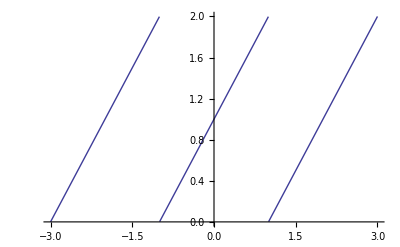

```mathematica
graphone=Plot[f[x],{x,-3,3},Exclusions->{-1,1}]
```

```mathematica
(*Manipulate[  consider manipulating k to find a reasonable value*)
```

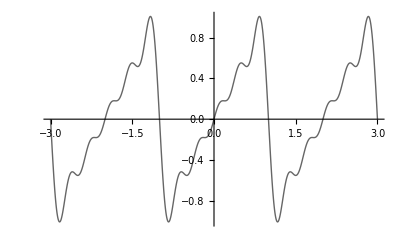

```mathematica
graphtwo=Plot[fourier[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

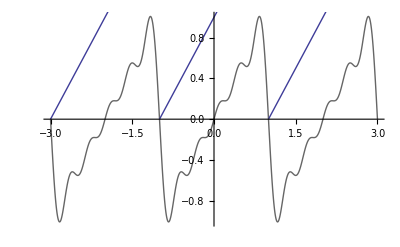

```mathematica
bothtwo=Show[graphtwo,graphone]
```

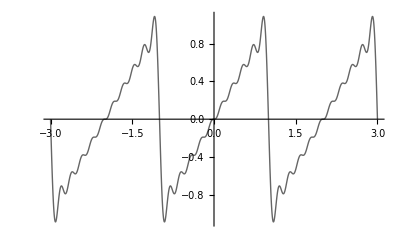

```mathematica
graphthree=Plot[fourier[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

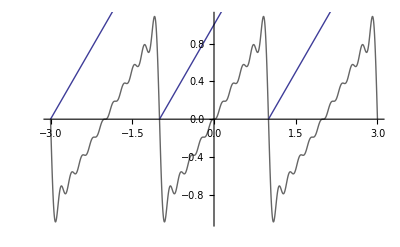

```mathematica
boththree=Show[graphthree,graphone]
```

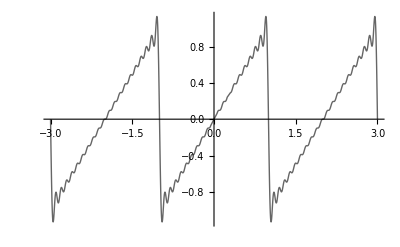

```mathematica
graphsix=Plot[fourier[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

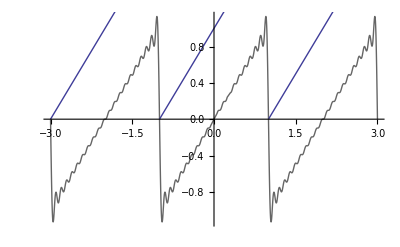

```mathematica
bothsix=Show[graphsix,graphone]
```

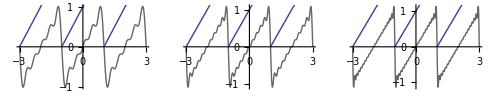

```mathematica
Show[GraphicsRow[{bothtwo,boththree,bothsix}]]
```